```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"C:\\Users\\Nanoplasmonics\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.05.1\\bin\\gswin64c.exe"
]*)
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
h c/1200
```

1.03392

```mathematica
lambdamin=250;
lambdamax=1300;
energyTicksMajor={1.03,1.24,1.55,2.07,3.1};
```

```mathematica
(*Esta función grafica el ajuste de Lorentz de la parte imaginaria de la función dieléctrica y los datos experimentales. Recibe funciones*)
plotLorentzFit[lorentz_,exp_,energyTicksMajor_,lambdamin_,lambdamax_,arriba1_,lateral1_,arriba2_,lateral2_]:=Module[{majorTicks,lorentzplot,expplot},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Curvas*)lorentzplot=Plot[lorentz[λ],{λ,lambdamin,lambdamax},PlotRange->All,PlotStyle->{RGBColor[6/255,151/255,213/255],Thickness[0.008]},PlotLegends->Placed[SwatchLegend[{Style["Ajuste de Lorentz",FontFamily->"Latin Modern Roman 10"]},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{lateral1,arriba1}]];
expplot=ListPlot[exp,PlotRange->All,PlotStyle->{RGBColor[232/255,68/255,42/255],FontFamily->"Latin Modern Roman 10"},PlotMarkers->{•},PlotLegends->Placed[SwatchLegend[{Style["Datos experimentales",FontFamily->"Latin Modern Roman 10"]},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{lateral2,arriba2}]];
(*Graficar*)Show[{lorentzplot,expplot},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\\mbox{Im}\\{\\varepsilon(\\omega)\\}"],Magnification->1.6],None},{Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},ImagePadding->{{90,10},{60,50}}]]

(*Esta función grafica la parte real  de la función dieléctrica obtenidos de KK.Recibe una lista de puntos*)
plotDielectricFunctionKKRe[parteRe_,energyTicksMajor_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)Plot[{Style[parteRe[λ],Blue]},{λ,lambdamin,lambdamax},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\mbox{Re}\{\varepsilon(\omega)\}"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,ImagePadding->{{70,10},{60,50}}]]

(*Esta función grafica la parte imaginaria  de la función dieléctrica obtenidos de KK*)
plotDielectricFunctionKKIm[parteIm_,energyTicksMajor_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)Plot[{Style[parteIm[λ],Red]},{λ,lambdamin,lambdamax},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\mbox{Im}\{\varepsilon(\omega)\}"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,ImagePadding->{{70,10},{60,50}}]]

(*Esta función grafica el ajuste de Lorentz de la parte imaginaria de la función dieléctrica y los datos experimentales. Recibe funciones*)
plotDielectricFunctionDifConcentrationsIm[qlist_List,energyTicksMajor_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)Plot[Evaluate@Table[ql[λ],{ql,qlist}],{λ,lambdamin,lambdamax},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\mbox{Im}\{\varepsilon(\omega)\}"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style["15.3",Magnification->1.2],Style["28.7",Magnification->1.2],Style["30.6",Magnification->1.2]},LegendMarkerSize->{15,5},LegendMargins->0,LegendLayout->{"Column",1},LegendLabel->Style["Concentración [g/dL]",FontFamily->"Latin Modern Roman 10",Magnification->1.2]],{0.7,0.65}]
,ImagePadding->{{70,10},{60,50}}]]

(*Esta función grafica el ajuste de Lorentz de la parte imaginaria de la función dieléctrica y los datos experimentales. Recibe funciones*)
plotDielectricFunctionDifConcentrationsRe[qlist_List,energyTicksMajor_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)Plot[Evaluate@Table[ql[λ],{ql,qlist}],{λ,lambdamin,lambdamax},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\mbox{Re}\{\varepsilon(\omega)\}"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style["15.3",Magnification->1.2],Style["28.7",Magnification->1.2],Style["30.6",Magnification->1.2]},LegendMarkerSize->{15,5},LegendMargins->0,LegendLayout->{"Column",2},LegendLabel->Style["Concentración [g/dL]",FontFamily->"Latin Modern Roman 10",Magnification->1.2]],{0.7,0.25}]
,ImagePadding->{{70,10},{60,50}}]]
```

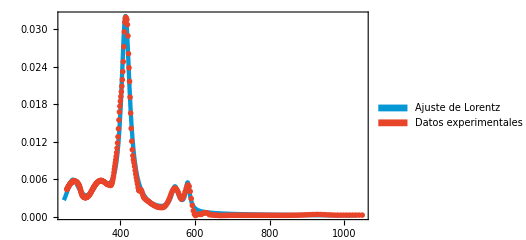

```mathematica
fit282[lambda_]:=fit28[h c/lambda]
eps282={h c/#[[1]],#[[2]]}&/@eps28Data;
energyTicksMajor28={  1.24,1.55,2.07,3.1};
plotLorentzFit[fit282,eps282,energyTicksMajor28,h c/5,h c/1.2,0.75,0.67,0.65,0.7]
```

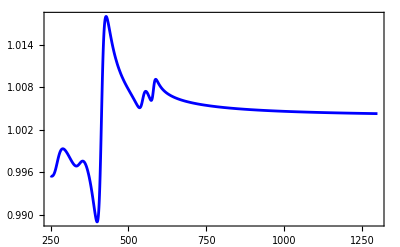

```mathematica
lambdas=Range[200,800,0.01];
parteRe281=Interpolation[Transpose[{omega,eps28KK[[1]]}]];
parteRe282[lambda_]:=parteRe281[h c/lambda];
plotDielectricFunctionKKRe[parteRe282,energyTicksMajor,lambdamin,lambdamax]
```

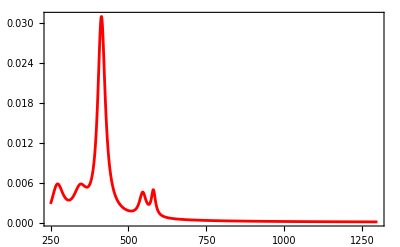

```mathematica
parteIm281=Interpolation[Transpose[{omega,eps28KK[[2]]}]];
parteIm282[lambda_]:=parteIm281[h c/lambda];
plotDielectricFunctionKKIm[parteIm282,energyTicksMajor,lambdamin,lambdamax]
```

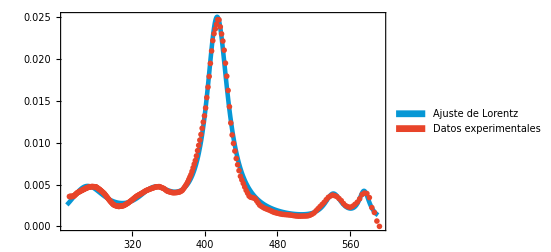

```mathematica
fit152[lambda_]:=fit15[h c/lambda]
eps152={h c/#[[1]],#[[2]]}&/@eps15Data;
energyTicksMajor15={2.26,2.48,2.76,3.1,3.55,4.14,5};
plotLorentzFit[fit152,eps152,energyTicksMajor15,h c/5,h c/2.1,0.85,0.73,0.75,0.76]
```

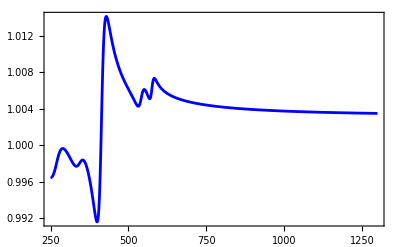

```mathematica
lambdas=Range[200,800,0.01];
parteRe151=Interpolation[Transpose[{omega,eps15KK[[1]]}]];
parteRe152[lambda_]:=parteRe151[h c/lambda];
plotDielectricFunctionKKRe[parteRe152,energyTicksMajor,lambdamin,lambdamax]
```

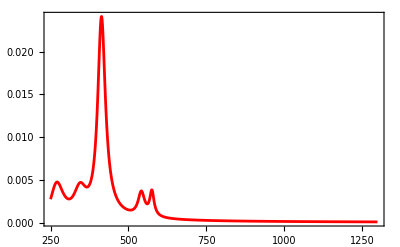

```mathematica
parteIm151=Interpolation[Transpose[{omega,eps15KK[[2]]}]];
parteIm152[lambda_]:=parteIm151[h c/lambda];
plotDielectricFunctionKKIm[parteIm152,energyTicksMajor,lambdamin,lambdamax]
```

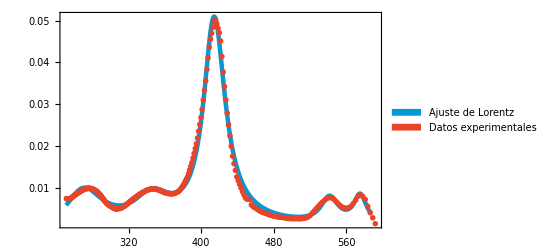

```mathematica
fit302[lambda_]:=fit30[h c/lambda]
eps302={h c/#[[1]],#[[2]]}&/@eps30Data;
energyTicksMajor30={2.26,2.48,2.76,3.1,3.55,4.14,5};
plotLorentzFit[fit302,eps302,energyTicksMajor30,h c/4.95,h c/2.11,0.85,0.73,0.75,0.76]
```

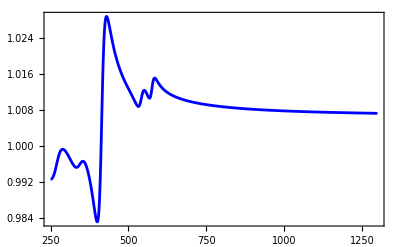

```mathematica
parteRe301=Interpolation[Transpose[{omega,eps30KK[[1]]}]];
parteRe302[lambda_]:=parteRe301[h c/lambda];
plotDielectricFunctionKKRe[parteRe302,energyTicksMajor,lambdamin,lambdamax]
```

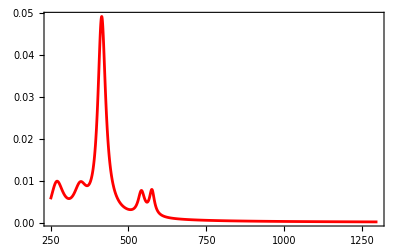

```mathematica
parteIm301=Interpolation[Transpose[{omega,eps30KK[[2]]}]];
parteIm302[lambda_]:=parteIm301[h c/lambda];
plotDielectricFunctionKKIm[parteIm302,energyTicksMajor,lambdamin,lambdamax]
```

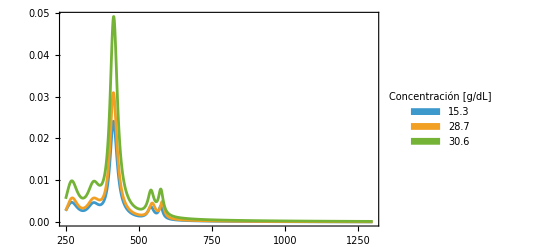

```mathematica
plotDielectricFunctionDifConcentrationsIm[{parteIm152,parteIm282,parteIm302},energyTicksMajor,lambdamin,lambdamax]
```

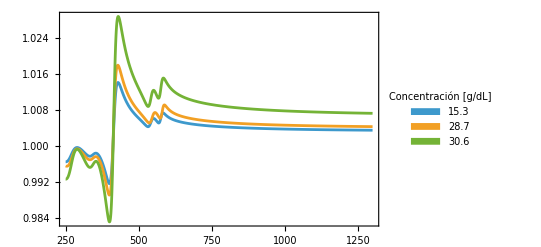

```mathematica
plotDielectricFunctionDifConcentrationsRe[{parteRe152,parteRe282,parteRe302},energyTicksMajor,lambdamin,lambdamax]
```

```mathematica
h c/1000
```

1.2407

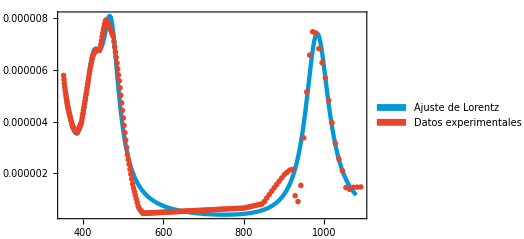

```mathematica
fitPlasma2[lambda_]:=fitPlasma[h c/lambda]
epsPlasma2={h c/#[[1]],#[[2]]}&/@epsPlasmaData;
energyTicksMajorPlasma={  1.24,1.38,1.55,1.77,2.07,2.48,3.1};
plotLorentzFit[fitPlasma2,epsPlasma2,energyTicksMajorPlasma,h c/3.5,h c/1.15,0.85,0.50,0.75,0.53]
```

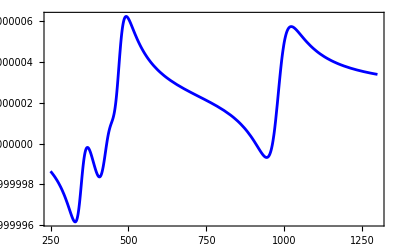

```mathematica
parteRePlasma1=Interpolation[Transpose[{omega,epsPlasmaKK[[1]]}]];
parteRePlasma2[lambda_]:=parteRePlasma1[h c/lambda];
plotDielectricFunctionKKRe[parteRePlasma2,energyTicksMajor,lambdamin,lambdamax]
```

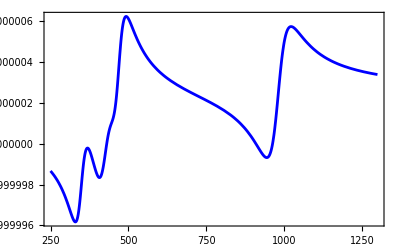

-Graphics-

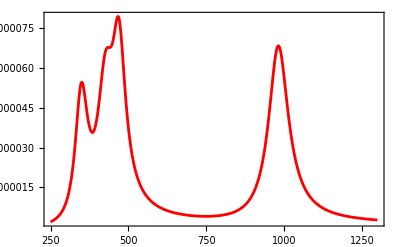

```mathematica
parteImPlasma1=Interpolation[Transpose[{omega,epsPlasmaKK[[2]]}]];
parteImPlasma2[lambda_]:=parteImPlasma1[h c/lambda];
plotDielectricFunctionKKIm[parteImPlasma2,energyTicksMajor,lambdamin,lambdamax]
```

## COMSOL - Mie

```mathematica
h c/300
```

4.13567

```mathematica
energyTicksMajorMie={1.24,1.38,1.55,1.77,2.06,2.48,3.10,4.14};
majorTicksMie=Module[{positionsMie},positionsMie=h c/#&/@energyTicksMajorMie;
Transpose[{positionsMie,energyTicksMajorMie}]];
```

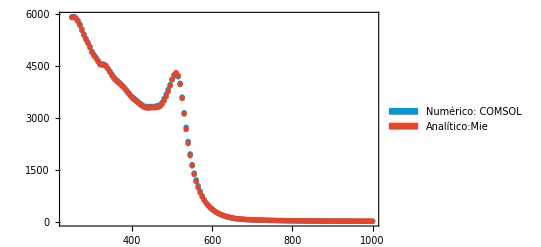

```mathematica
ListPlot[{Style[au30LambdaCabs,RGBColor[6/255,151/255,213/255]],Style[auCabsMie,RGBColor[232/255,68/255,42/255]]},PlotRange->All,PlotStyle->{FontFamily->"Latin Modern Roman 10"},PlotMarkers->{•},PlotLegends->Placed[SwatchLegend[{Style["Numérico: COMSOL",FontFamily->"Latin Modern Roman 10"],Style["Analítico:Mie",FontFamily->"Latin Modern Roman 10"]},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.3],{0.7,0.8}],Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["C_{abs}[\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicksMie}},ImagePadding->{{90,10},{60,50}}]
```

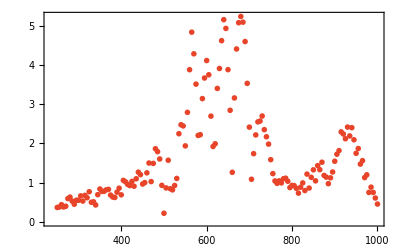

```mathematica
ListPlot[Style[Transpose[{lambdadatosAu30lambda,(Abs[au30LambdaCabs[[All,2]]-auCabsMie[[All,2]]]/au30LambdaCabs[[All,2]])*100}],RGBColor[232/255,68/255,42/255]],PlotRange->All,PlotStyle->{FontFamily->"Latin Modern Roman 10"},PlotMarkers->{•},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["|C_{COMSOL}-C_{Mie}|[\%]"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicksMie}},ImagePadding->{{90,10},{60,50}}]
```

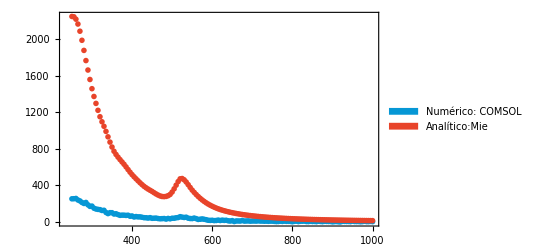

```mathematica
ListPlot[{Style[au30LambdaCsca,RGBColor[6/255,151/255,213/255]],Style[auCscaMie,RGBColor[232/255,68/255,42/255]]},PlotRange->All,PlotStyle->{FontFamily->"Latin Modern Roman 10"},PlotMarkers->{•},PlotLegends->Placed[SwatchLegend[{Style["Numérico: COMSOL",FontFamily->"Latin Modern Roman 10"],Style["Analítico:Mie",FontFamily->"Latin Modern Roman 10"]},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.3],{0.7,0.8}],Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["C_{sca}[\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicksMie}},ImagePadding->{{90,10},{60,50}}]
```

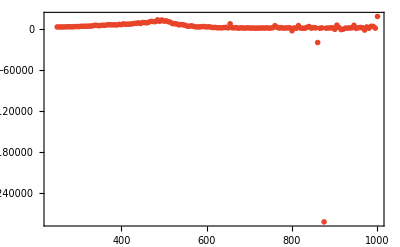

```mathematica
ListPlot[Style[Transpose[{lambdadatosAu30lambda,(Abs[au30LambdaCsca[[All,2]]-auCabsMie[[All,2]]]/au30LambdaCsca[[All,2]])*100}],RGBColor[232/255,68/255,42/255]],PlotRange->All,PlotStyle->{FontFamily->"Latin Modern Roman 10"},PlotMarkers->{•},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["|C_{COMSOL}-C_{Mie}|[\%]"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicksMie}},ImagePadding->{{90,10},{60,50}}]
```